# Classical limit

```mathematica
Quit[]
```

## Resources

### IGraphM

```mathematica
(* Install Igraph the first time around, downloading it first from https://github.com/szhorvat/IGraphM/releases/download/v0.6.5/IGraphM-0.6.5.paclet *)
(*
Needs["PacletManager`"]
PacletInstall["~/Downloads/IGraphM-0.6.5.paclet"]
*)
```

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

Testing graph isomorphisms

```mathematica
ga=Graph[{1<->2,1<->2,2<->3}];
gb=Graph[{a<->b,a<->b,b<->c}];
```

```mathematica
(* Sadly built-in Mathematica Iso check sucks *)
IsomorphicGraphQ[ga,gb]
```

IsomorphicGraphQ::ngen: The generalized … is not implemented.

IsomorphicGraphQ[-Graphics-,-Graphics-]


{-Graphics-,VertexColors→{0,0,0},EdgeColors→{2,1}}

```mathematica
IGColoredSimpleGraph[gb]
```

```mathematica
(* But the one from IGraph does the job using edge colouring *)
IGVF2IsomorphicQ[IGColoredSimpleGraph[ga],IGColoredSimpleGraph[gb]]
```

True

### Signature assignment

```mathematica
ToUndirectedGraph[g_,OptionsPattern[{KeepOnlyEdgeIDs->False,SortVertices->False}]]:=Graph[Table[e/.{DirectedEdge[a_,b_,props__]:>UndirectedEdge@@Join[
If[OptionValue[SortVertices],Sort[{a,b}],{a,b}],
{If[OptionValue[KeepOnlyEdgeIDs],<|"id"->props["id"]|>,props]}
]},{e,EdgeList[g]}]]
```

```mathematica
MakeAllExternalLegsIncoming[g_]:=Module[
{
OutgoingEdgesIndices
},
OutgoingEdgesIndices=Map[EdgeIndex[g,#⟦2⟧⟦1⟧]&,Select[Table[{iV,EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]]},{iV, VertexList[g]}],And[Length[#⟦2⟧]==1,EdgeCount[#⟦2⟧,DirectedEdge[_,#⟦1⟧,___]]==1]&]];
{OutgoingEdgesIndices,DirectedGraph[
Table[If[MemberQ[OutgoingEdgesIndices,ie],
EdgeList[g]⟦ie⟧/.{DirectedEdge[x_,y_,z___]:>DirectedEdge[y,x,z]},
EdgeList[g]⟦ie⟧
],{ie,Length[EdgeList[g]]}]
]}
]
```

```mathematica
cFFAssignSignaturesStartingFromEdge[g_Graph,startingVertex_,InputSignatures_]:=Module[
{allIncomingEdges,allOutgoingEdges,otherVertexAndDirection,edgesWithoutSignature,signatures,edgesWithSignature},
signatures=Association[Table[k->InputSignatures[k],{k,Keys[InputSignatures]}]];
allIncomingEdges=EdgeList[g,DirectedEdge[_,startingVertex,_]];
allOutgoingEdges=EdgeList[g,DirectedEdge[startingVertex,_,_]];
edgesWithoutSignature=Select[Join[allIncomingEdges,allOutgoingEdges],Not[MemberQ[Keys[signatures],#]]&];
edgesWithSignature=Select[Join[allIncomingEdges,allOutgoingEdges],MemberQ[Keys[signatures],#]&];
If[And[Length[edgesWithoutSignature]==1,Length[edgesWithSignature]>0],
Do[
otherVertexAndDirection=e/.{
DirectedEdge[startingVertex,a_,_]:>{a,1},
DirectedEdge[a_,startingVertex,_]:>{a,-1}
};
AssociateTo[signatures,e->(otherVertexAndDirection[[2]]*(Total[Table[signatures[eIN],{eIN,Select[allIncomingEdges,MemberQ[Keys[signatures],#]&]}]]-Total[Table[signatures[eOUT],{eOUT,Select[allOutgoingEdges,MemberQ[Keys[signatures],#]&]}]]))];
signatures=cFFAssignSignaturesStartingFromEdge[g,otherVertexAndDirection[[1]],signatures];,{e,edgesWithoutSignature}];
];

signatures
]
```

```mathematica
cFFGetEdgeSignatures[g_Graph,OptionsPattern[{lmb->Automatic,forceExternalVertices->Automatic}]]:=Module[
{spanningTree,selectedLMB,leaves,startEdge,signatures,externalVertices,externalEdges,tmpA,leafEdge,undirectedGraph,selfLoop,nonSelfLoop},
externalVertices=If[OptionValue[forceExternalVertices]===Automatic,
Sort[Select[VertexList[g],VertexDegree[g,#]===1&]],
OptionValue[forceExternalVertices]
];
If[OptionValue[lmb]===Automatic,
(*spanningTree=FindSpanningTree[ToUndirectedGraph[g]];*)
selfLoop=EdgeList[g,DirectedEdge[x_,x_,__]];
nonSelfLoop=Select[EdgeList[g],Not[MemberQ[selfLoop,#]]&];
undirectedGraph=ToUndirectedGraph[Graph[nonSelfLoop]];
(* This is necessary to get around of bug of FindSpanningTree when called with a Tree graph, fuck mathematica... *)
If[Length[FindCycle[undirectedGraph]]==0,
spanningTree=nonSelfLoop;
,
spanningTree=Select[nonSelfLoop,MemberQ[
Table[e/.{UndirectedEdge[_,_,props_]:>props["id"]},{e,EdgeList[FindSpanningTree[undirectedGraph]]}],
GetEdgeProperty[#,"id"]]&];
];
(*spanningTree=Select[EdgeList[g],MemberQ[
Table[e/.{UndirectedEdge[_,_,props_]:>props["id"]},{e,EdgeList[FindSpanningTree[ToUndirectedGraph[g]]]}],
GetEdgeProperty[#,"id"]]&];*)
selectedLMB=SortBy[Complement[EdgeList[g],EdgeList[spanningTree]],(#/.{DirectedEdge[a_,b_,name_]:>name})&];
,
spanningTree=DirectedGraph[Select[EdgeList[g],Not[MemberQ[OptionValue[lmb],GetEdgeProperty[#,"id"]]]&]];
selectedLMB=SortBy[Select[EdgeList[g],MemberQ[OptionValue[lmb],GetEdgeProperty[#,"id"]]&],Position[OptionValue[lmb],GetEdgeProperty[#,"id"]][[1]][[1]]&];
];

(*Assign signatures to externals now*)
signatures=Association[Table[tmpA=EdgeList[g,DirectedEdge[externalVertices[[iev]],_,_]];
(*It is much simpler if we force all externals incoming so check for this here*)
If[Length[tmpA]!=1,Print["ERROR: please define all externals as incoming in your topology."];Return[Null];];
tmpA=If[Length[tmpA]==1,tmpA[[1]],EdgeList[g,DirectedEdge[_,externalVertices[[iev]],_]][[1]]];
tmpA->{Table[0,{i,Length[selectedLMB]}],Table[If[iev===j,1,0],{j,Length[externalVertices]}]},{iev,Length[externalVertices]}]];

(*And LMB edges now*)
signatures=AssociateTo[signatures,Table[selectedLMB[[ie]]->{Table[If[ie===j,1,0],{j,Length[selectedLMB]}],Table[0,{i,Length[externalVertices]}]},{ie,Length[selectedLMB]}]];

(*And all others now*)
leaves=Select[VertexList[spanningTree],And[VertexDegree[spanningTree,#]===1,True(*Not[VertexDegree[g,#]===1]*)]&];

leaves=Table[
leafEdge=EdgeList[spanningTree,DirectedEdge[leaf,_,_]];

If[Length[leafEdge]==1,
leafEdge=leafEdge[[1]];
If[MemberQ[Keys[signatures],leafEdge],
leafEdge/.{DirectedEdge[_,x_,_]:>x},
leaf
]
,
leafEdge=EdgeList[spanningTree,DirectedEdge[_,leaf,_]][[1]];

If[MemberQ[Keys[signatures],leafEdge],
leafEdge/.{DirectedEdge[x_,_,_]:>x},
leaf
]
],{leaf,leaves}];

leaves=DeleteDuplicates[leaves];

Do[signatures=cFFAssignSignaturesStartingFromEdge[g,leaf,signatures];,{leaf,leaves}];

signatures]
```

```mathematica
AssignSignatures[INg_Graph,OptionsPattern[{lmb->Automatic,forceExternalVertices->Automatic}]]:=Module[
{g,signatures,flippedExternalEdgeIndices,flippedG,t,edge,externalFlips,signaturesFlipped},
t=MakeAllExternalLegsIncoming[INg];
flippedExternalEdgeIndices=t⟦1⟧;
flippedG=t⟦2⟧;

g=DirectedGraph[Table[EdgeList[flippedG][[ie]]/.{DirectedEdge[a_,b_]:>DirectedEdge[a,b,ie]},{ie,Length[EdgeList[flippedG]]}]];

signatures=cFFGetEdgeSignatures[g,lmb->OptionValue[lmb],forceExternalVertices->OptionValue[forceExternalVertices]];

externalFlips=Table[Position[signatures[EdgeList[g]⟦ie⟧]⟦2⟧,1]⟦1⟧⟦1⟧,{ie,
Select[flippedExternalEdgeIndices,Or[OptionValue[forceExternalVertices]===Automatic,MemberQ[OptionValue[forceExternalVertices],(EdgeList[g]⟦#⟧/.{DirectedEdge[a_,_,__]:>a})]]&]}];

signaturesFlipped=Association[Table[edge->{signatures[edge]⟦1⟧,Table[
If[MemberQ[externalFlips,is],-signatures[edge]⟦2⟧⟦is⟧,signatures[edge]⟦2⟧⟦is⟧]
,{is,Length[signatures[edge]⟦2⟧]}]},{edge,Keys[signatures]}]];

If[Not[OptionValue[forceExternalVertices]===Automatic],
Do[
edge=EdgeList[g]⟦ie⟧;
If[And[MemberQ[flippedExternalEdgeIndices,ie],Not[MemberQ[OptionValue[forceExternalVertices],edge/.{DirectedEdge[a_,_,__]:>a}]]],
AssociateTo[signatures,
edge->{Table[-s,{s,signaturesFlipped[edge]⟦1⟧}],Table[-s,{s,signaturesFlipped[edge]⟦2⟧}]}
];
];
,{ie,Length[EdgeList[g]]}];
];
DirectedGraph[Table[
edge=EdgeList[g]⟦ie⟧;
edge/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[
If[MemberQ[flippedExternalEdgeIndices,ie],b,a],
If[MemberQ[flippedExternalEdgeIndices,ie],a,b],
Association[Join[
Table[p->props[p],{p,Keys[props]}],
{"sig"->If[MemberQ[flippedExternalEdgeIndices,ie],
signatures[edge],signaturesFlipped[edge]]}
]]
]},{ie,Length[EdgeList[g]]}]]
]
```

```mathematica
(* Example call to the above *)
```

```mathematica
(*
ShowClassicalGraph[AssignSignatures[Graph[{{1, "topIN"}, {3, "top"}, {2, "topOUT"}, {1, "botIN"}, {3, "bot"}, {2, "botOUT"}}, {DirectedEdge[{1, "topIN"}, {3, "top"}, <|"id" -> {1, "topIN"}, "sig" -> {{0, 0, 0}, {0, 1}}|>], DirectedEdge[{3, "top"}, {2, "topOUT"}, <|"id" -> {2, "topOUT"}, "sig" -> {{-1, 0, 0}, {0, 1}}|>], DirectedEdge[{1, "botIN"}, {3, "bot"}, <|"id" -> {1, "botIN"}, "sig" -> {{0, 0, 0}, {1, 0}}|>], DirectedEdge[{3, "bot"}, {2, "botOUT"}, <|"id" -> {2, "botOUT"}, "sig" -> {{1, 0, 0}, {1, 0}}|>], DirectedEdge[{3, "top"}, {3, "bot"}, <|"id" -> {1, {"blob", 1, 1}}, "sig" -> {{1, 0, 0}, {0, 0}}|>], DirectedEdge[{3, "bot"}, {3, "bot"}, <|"id" -> {1, {"blob", 2, 1}}, "sig" -> {{0, 1, 0}, {0, 0}}|>], DirectedEdge[{3, "bot"}, {3, "bot"}, <|"id" -> {1, {"blob", 3, 1}}, "sig" -> {{0, 0, 1}, {0, 0}}|>]}],
forceExternalVertices->{{1, "topIN"}, {1, "botIN"}, {2, "topOUT"}}
]]
*)
```

```mathematica
(*ShowClassicalGraph[AssignSignatures[
Graph[{{1, "topIN"}, {3, "top"}, {4, "top"}, {2, "topOUT"}, {1, "botIN"}, {3, "bot"}, {4, "bot"}, {2, "botOUT"}}, {DirectedEdge[{1, "topIN"}, {3, "top"}, <|"id" -> {1, "topIN"}|>], DirectedEdge[{3, "top"}, {4, "top"}, <|"id" -> {3, "top"}|>], DirectedEdge[{4, "top"}, {2, "topOUT"}, <|"id" -> {2, "topOUT"}|>], DirectedEdge[{1, "botIN"}, {3, "bot"}, <|"id" -> {1, "botIN"}|>], DirectedEdge[{3, "bot"}, {4, "bot"}, <|"id" -> {3, "bot"}|>], DirectedEdge[{4, "bot"}, {2, "botOUT"}, <|"id" -> {2, "botOUT"}|>], DirectedEdge[{3, "top"}, {3, "bot"}, <|"id" -> {1, {"blob", 1, 1}}|>], DirectedEdge[{4, "top"}, {4, "bot"}, <|"id" -> {1, {"blob", 2, 1}}|>]}],
lmb->{{1, {"blob", 1, 1}}, {1, {"blob", 2, 1}}},
forceExternalVertices->{{1,"botIN"},{1,"topIN"}}]]*)
```

```mathematica
(*ggg=Graph[{{1, "topIN"}, {3, "top"}, {2, "topOUT"}, {1, "botIN"}, {3, "bot"}, {2, "botOUT"}}, {DirectedEdge[{1, "topIN"}, {3, "top"}, <|"id" -> {1, "topIN"}|>], DirectedEdge[{3, "top"}, {2, "topOUT"}, <|"id" -> {2, "topOUT"}|>], DirectedEdge[{1, "botIN"}, {3, "bot"}, <|"id" -> {1, "botIN"}|>], DirectedEdge[{3, "bot"}, {2, "botOUT"}, <|"id" -> {2, "botOUT"}|>], DirectedEdge[{3, "top"}, {3, "bot"}, <|"id" -> {1, {"blob", 1, 1}}|>]}];
ShowClassicalGraph[AssignSignatures[ggg]]*)
```

```mathematica
(*
ShowClassicalGraph[AssignSignatures[
Graph[{{1, "topIN"}, {3, "top"}, {2, "topOUT"}, {1, "botIN"}, {3, "bot"}, {4, "bot"}, {5, "bot"}, {6, "bot"}, {7, "bot"}, {2, "botOUT"}}, {DirectedEdge[{1, "topIN"}, {3, "top"}, <|"id" -> {1, "topIN"}|>], DirectedEdge[{3, "top"}, {2, "topOUT"}, <|"id" -> {2, "topOUT"}|>], DirectedEdge[{1, "botIN"}, {3, "bot"}, <|"id" -> {1, "botIN"}|>], DirectedEdge[{3, "bot"}, {4, "bot"}, <|"id" -> {3, "bot"}|>], DirectedEdge[{4, "bot"}, {5, "bot"}, <|"id" -> {4, "bot"}|>], DirectedEdge[{5, "bot"}, {6, "bot"}, <|"id" -> {5, "bot"}|>], DirectedEdge[{6, "bot"}, {7, "bot"}, <|"id" -> {6, "bot"}|>], DirectedEdge[{7, "bot"}, {2, "botOUT"}, <|"id" -> {2, "botOUT"}|>], DirectedEdge[{3, "top"}, {3, "bot"}, <|"id" -> {1, {"blob", 1, 1}}|>], DirectedEdge[{4, "bot"}, {6, "bot"}, <|"id" -> {1, {"blob", 2, 1}}|>], DirectedEdge[{5, "bot"}, {7, "bot"}, <|"id" -> {1, {"blob", 3, 1}}|>]}],
forceExternalVertices->{{1, "botIN"}, {1, "topIN"}, {2, "topOUT"}}
]]
*)
```

### Graph Manipulation

```mathematica
GetEdgeProperty[edge_,prop_]:=(edge/.{DirectedEdge[_,_,props_]:>props})[prop]
```

```mathematica
ShowClassicalGraph[g_Graph,OptionsPattern[{Size->{500,500},vLabels->Automatic,eLabels->Automatic,EdgeColours-><|1->Red,2->Darker[Green],3->Purple,4->Orange,5->Darker[Yellow]|>,Highlight->True,highlightCut->None}]]:=Module[{nonCutEdges},
If[OptionValue[highlightCut]===None,
nonCutEdges=EdgeList[g];,
nonCutEdges=Select[EdgeList[g],Not[MemberQ[OptionValue[highlightCut]⟦1⟧,GetEdgeProperty[#,"id"]]]&];
];
DirectedGraph[EdgeList[g],
ImageSize->OptionValue[Size],VertexLabels->OptionValue[vLabels],EdgeLabels->If[Or[OptionValue[eLabels]===None,OptionValue[eLabels]===Automatic],OptionValue[eLabels],
If[StringQ[OptionValue[eLabels]],
Table[e->GetEdgeProperty[e,OptionValue[eLabels]],{e,EdgeList[g]}],
OptionValue[eLabels]
]
],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},
EdgeStyle->If[OptionValue[Highlight],Join[
Table[
edge->OptionValue[EdgeColours][GetEdgeProperty[edge,"id"]⟦2⟧⟦2⟧]
,{edge,Select[nonCutEdges,And[ListQ[GetEdgeProperty[#,"id"]],ListQ[GetEdgeProperty[#,"id"]⟦2⟧],GetEdgeProperty[#,"id"]⟦2⟧⟦1⟧=="blob"]&]}
],
Table[
edge-> Directive[Blue,Thickness[0.002]]
,{edge,Select[nonCutEdges,And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="top"]&]}
],
Table[
edge-> Directive[Darker[Darker[Blue]],Thickness[0.002]]
,{edge,Select[nonCutEdges,And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="bot"]&]}
],
Table[
edge-> OptionValue[highlightCut]⟦2⟧,
{edge,Complement[EdgeList[g],nonCutEdges]}
]
],Automatic],
VertexCoordinates->If[OptionValue[Highlight],{
{1,"topIN"}->{0,1},{2,"topOUT"}->{1,1},
{1,"botIN"}->{0,0},{2,"botOUT"}->{1,0}
},Automatic]
]
]
```

```mathematica
ShowClassicalGraphs[graphs_,OptionsPattern[{Ncolumns->3,Size->{500,500},HeaderHeight->10,vLabels->Automatic,eLabels->None}]]:=Grid[Table[
Table[
Column[{Panel[Text[Style["Graph #"<>ToString[OptionValue[Ncolumns]i+ig+1],FontSize->13]],Alignment->Center,ImageSize->{OptionValue[Size]⟦1⟧,OptionValue[HeaderHeight]}],ShowClassicalGraph[graphs⟦OptionValue[Ncolumns]i+ig+1⟧,Size->OptionValue[Size],eLabels->OptionValue[eLabels],vLabels->OptionValue[vLabels]]}],
{ig,Range[0,Length[graphs⟦OptionValue[Ncolumns]i+1;;Min[OptionValue[Ncolumns](i+1),Length[graphs]]⟧]-1]}],{i,0,Floor[Length[graphs]/OptionValue[Ncolumns]]}]]
```

```mathematica
ShowEquivalenceClasses[classes_,OptionsPattern[{Ncolumns->3,Size->{500,500},HeaderHeight->10,vLabels->Automatic,eLabels->None,ShowOriginatingGraph->False}]]:=Grid[
Table[
Table[
Column[{Panel[Text[Style["Class #"<>ToString[OptionValue[Ncolumns]i+ig+1]<>" ("<>ToString[Length[classes[Keys[classes]⟦OptionValue[Ncolumns]i+ig+1⟧]]]<>" graphs)",FontSize->13]],Alignment->Center,ImageSize->{OptionValue[Size]⟦1⟧,OptionValue[HeaderHeight]}],
ShowClassicalGraph[
If[OptionValue[ShowOriginatingGraph],
Keys[classes]⟦OptionValue[Ncolumns]i+ig+1⟧⟦2⟧,
classes[Keys[classes]⟦OptionValue[Ncolumns]i+ig+1⟧]⟦1⟧
],
Size->OptionValue[Size],eLabels->OptionValue[eLabels],vLabels->OptionValue[vLabels]]}],
{ig,Range[0,Length[Keys[classes]⟦OptionValue[Ncolumns]i+1;;Min[OptionValue[Ncolumns](i+1),Length[Keys[classes]]]⟧]-1]}],
{i,0,Floor[Length[Keys[classes]]/OptionValue[Ncolumns]]}]]
```

```mathematica
GeneralizedStringJoin[strings_]:=Apply[StringJoin,ToString[#,StandardForm]&/@strings]
```

```mathematica
ShowCuts[graph_,cuts_,OptionsPattern[{Ncolumns->3,Size->{500,500},HeaderHeight->10,vLabels->Automatic,eLabels->None,cutColor->Darker[Darker[Red]],cutThickness->0.01}]]:=Grid[Table[
Table[
Column[{Panel[Text[Style[
GeneralizedStringJoin[{"Cut #",Style[ToString[OptionValue[Ncolumns]i+ig+1],Darker[Red]]," (",Style[ToString[Length[cuts⟦OptionValue[Ncolumns]i+ig+1⟧]],Darker[Blue]],"-cut",") ",Style[" [ ",Red],GeneralizedStringJoin[Riffle[Table[ToString[c],{c,cuts⟦OptionValue[Ncolumns]i+ig+1⟧}],Style[" | ",Red]]],Style[" ]",Red]}]
,FontSize->13]],Alignment->Center,ImageSize->{OptionValue[Size]⟦1⟧,OptionValue[HeaderHeight]}],ShowClassicalGraph[graph,Size->OptionValue[Size],eLabels->OptionValue[eLabels],vLabels->OptionValue[vLabels],
 highlightCut->{cuts⟦OptionValue[Ncolumns]i+ig+1⟧,Directive[OptionValue[cutColor],Thickness[OptionValue[cutThickness]]]}
 ]}],
{ig,Range[0,Length[cuts⟦OptionValue[Ncolumns]i+1;;Min[OptionValue[Ncolumns](i+1),Length[cuts]]⟧]-1]}],{i,0,Floor[Length[cuts]/OptionValue[Ncolumns]]}]]
```

```mathematica
ConvertToSimpleGraph[g_]:=Module[{multiplicityMap,sortedVertices,newEdges},
multiplicityMap=<||>;
newEdges={};
Do[
sortedVertices=e/.{DirectedEdge[a_,b_,__]:>Sort[{a,b}]};
If[Not[MemberQ[Keys[multiplicityMap],sortedVertices]],
AssociateTo[multiplicityMap,sortedVertices->1];
AppendTo[newEdges,e];
,
AssociateTo[multiplicityMap,sortedVertices->multiplicityMap[sortedVertices]+1];
];
,{e,EdgeList[g]}
];
DirectedGraph[Table[
e/.{DirectedEdge[a_,b_,prop_]:>
DirectedEdge[a,b,
Association[Join[Table[k->prop[k],{k,Keys[prop]}],{"multiplicity"->multiplicityMap[Sort[{a,b}]]}]]
]
}
,{e,newEdges}]]
]
```

```mathematica
ColorGraph[g_,OptionsPattern[{taggedEdges->None,taggedVertices->None}]]:=Module[{coloredGraph,vColors,eColors,vTag,eTag},
coloredGraph=IGColoredSimpleGraph[ToUndirectedGraph[g]];
vColors=coloredGraph⟦2⟧⟦2⟧;
eColors=coloredGraph⟦3⟧⟦2⟧;

If[Not[OptionValue[taggedVertices]===None],
Do[If[MemberQ[Keys[OptionValue[taggedVertices]],VertexList[g]⟦iv⟧],vColors⟦iv⟧= vColors⟦iv⟧+OptionValue[taggedVertices][VertexList[g]⟦iv⟧];],{iv,Length[VertexList[g]]}];
];
If[Not[OptionValue[taggedEdges]===None],
Do[If[MemberQ[Keys[OptionValue[taggedEdges]],GetEdgeProperty[EdgeList[g]⟦ie⟧,"id"]],eColors⟦ie⟧=eColors⟦ie⟧+OptionValue[taggedEdges][GetEdgeProperty[EdgeList[g]⟦ie⟧,"id"]];],{ie,Length[EdgeList[coloredGraph⟦1⟧]]}];
];
{coloredGraph⟦1⟧,VertexColors->vColors,EdgeColors->eColors}
]
```

```mathematica
Is1PI[g_]:=Module[{treeSigs},
treeSigs=Table[s⟦2⟧,{s,Select[Table[GetEdgeProperty[e,"sig"],{e,EdgeList[g]}],AllTrue[#⟦1⟧,Function[s,s==0]]&]}];
Length[DeleteDuplicatesBy[treeSigs,Sort[{#,Table[-s,{s,#}]}]&]]<Length[treeSigs]
]
```

```mathematica
GenerateLoopGraphs[blobs_, OptionsPattern[{
symmmetrizeTopLine->True,symmmetrizeBotLine->True,topNPropRange->Automatic,botNPropRange->Automatic,
nLoops->2,tagExternal->False,tagBlobs->False,tagBlobType->False,tagTopLine->False,tagBotLine->False, Only1PI->False,
MarkTopLine->True,MarkBotLine->True
}]]:=Module[{
topMassiveLines, botMassiveLines, allGraphs, nIter, maxIter,
 allBlobCombinations,topTopo,botTopo,blobComb,externalBlobVertices,massiveVertices,newGraph, sewingMap,reverseSewingMap,
iExternal,allColoredRepr, coloredRepr,tPropRange,bPropRange,aVertex, edgeColors, vertexColors, permutations,
blobsEdges,sewingOrder,definingAttachments,iTopAttachment,iBotAttachment
},

tPropRange=If[
Not[OptionValue[topNPropRange]===Automatic],
OptionValue[topNPropRange],
{0,2*OptionValue[nLoops]}
];

bPropRange=If[
Not[OptionValue[botNPropRange]===Automatic],
OptionValue[botNPropRange],
{0,2*OptionValue[nLoops]}
];

(* Enumerat possible topologies of top and bot massive lines at 2-loop *)
topMassiveLines= Table[
DirectedGraph[
Join[{
DirectedEdge[{1,"topIN"},{3,"top"},<|"id"->{1,"topIN"}|>]
},
Table[
DirectedEdge[{iProp+2,"top"},{iProp+3,"top"},<|"id"->{iProp+2,"top"}|>],{iProp,1,nProp}],
{
DirectedEdge[{nProp+3,"top"},{2,"topOUT"},<|"id"->{2,"topOUT"}|>]
}
]
],
{nProp,tPropRange⟦1⟧,tPropRange⟦2⟧}];

botMassiveLines= Table[
DirectedGraph[
Join[{
DirectedEdge[{1,"botIN"},{3,"bot"},<|"id"->{1,"botIN"}|>]
},
Table[
DirectedEdge[{iProp+2,"bot"},{iProp+3,"bot"},<|"id"->{iProp+2,"bot"}|>],{iProp,1,nProp}],
{
DirectedEdge[{nProp+3,"bot"},{2,"botOUT"},<|"id"->{2,"botOUT"}|>]
}
]
],
{nProp,bPropRange⟦1⟧,bPropRange⟦2⟧}];

(* Now loop over all top line, bot lines and blob topologies, and generate graphs this way. Not the most efficient by far but it works *)

allGraphs={};
allColoredRepr={};
nIter=0;
allBlobCombinations=Join@@Table[
DeleteDuplicates[Table[Sort[c],{c,Tuples@Table[Range[Length[blobs]],{i,nBlobs}]}]],
{nBlobs,1,OptionValue[nLoops]+1}];

maxIter=Length[allBlobCombinations]Length[topMassiveLines]Length[botMassiveLines];
Monitor[
Do[
topTopo=topMassiveLines⟦iTopTopology⟧;
Do[
botTopo=botMassiveLines⟦iBotTopology⟧;
Do[
blobComb=Table[blobs[[iBlob]],{iBlob,allBlobCombinations⟦iBlobCombination⟧}];
nIter+=1;

(* First make sure there is the right number of vertices to glue *)
If[
(Length[VertexList[topTopo]]-2)+(Length[VertexList[botTopo]]-2)!=Total[Table[Length[blob["external_vertices"]],{blob,blobComb}]],
Continue[];
];
externalBlobVertices=Join@@Table[Table[{vertex,iBlob},{vertex,blobComb⟦iBlob⟧["external_vertices"]}],{iBlob,1,Length[blobComb]}];
massiveVertices=Join[Table[(e/.{DirectedEdge[a_,b_,__]:>a}),{e,EdgeList[topTopo]⟦2;;⟧}],Table[(e/.{DirectedEdge[a_,b_,__]:>a}),{e,EdgeList[botTopo]⟦2;;⟧}]];
(* Now sew the vertices of the massive lines with the blob extrnal vertices in all possible ways, but ignoring top or bottom permutations if symmetrized *)
definingAttachments=Join[
Table[If[OptionValue[symmmetrizeTopLine],"top",iTopEdge],{iTopEdge,Length[EdgeList[topTopo]⟦2;;⟧]}],
Table[If[OptionValue[symmmetrizeBotLine],"bot",iBotEdge],{iBotEdge,Length[EdgeList[topTopo]⟦2;;⟧]+1,Length[EdgeList[topTopo]⟦2;;⟧]+Length[EdgeList[botTopo]⟦2;;⟧]}]
];

permutations=Permutations[definingAttachments];

Do[
sewingOrder=permutations⟦iPerm⟧;
sewingMap=<||>;
reverseSewingMap=<||>;

iTopAttachment=0;
iBotAttachment=Length[EdgeList[topTopo]⟦2;;⟧];
Do[
If[sewingOrder⟦ip⟧=="top",
iTopAttachment+=1;
AssociateTo[sewingMap,externalBlobVertices⟦ip⟧->massiveVertices⟦iTopAttachment⟧];
AssociateTo[reverseSewingMap,massiveVertices⟦iTopAttachment⟧->externalBlobVertices⟦ip⟧];
,
If[sewingOrder⟦ip⟧=="bot",
iBotAttachment+=1;
AssociateTo[sewingMap,externalBlobVertices⟦ip⟧->massiveVertices⟦iBotAttachment⟧];
AssociateTo[reverseSewingMap,massiveVertices⟦iBotAttachment⟧->externalBlobVertices⟦ip⟧];
,
AssociateTo[sewingMap,externalBlobVertices⟦ip⟧->massiveVertices⟦sewingOrder⟦ip⟧⟧];
AssociateTo[reverseSewingMap,massiveVertices⟦sewingOrder⟦ip⟧⟧->externalBlobVertices⟦ip⟧];
];
];
,{ip,Length[sewingOrder]}];

blobsEdges=Table[Table[
edge/.{
DirectedEdge[a_,b_,__]:>
DirectedEdge[
If[MemberQ[Keys[sewingMap],{a,iBlob}],sewingMap[{a,iBlob}],{a,iBlob,blobComb⟦iBlob⟧["id"]}],
If[MemberQ[Keys[sewingMap],{b,iBlob}],sewingMap[{b,iBlob}],{b,iBlob,blobComb⟦iBlob⟧["id"]}],
<|"id"->{GetEdgeProperty[edge,"id"],{"blob",iBlob,blobComb⟦iBlob⟧["id"]}}|>]
}
,{edge,EdgeList[blobComb⟦iBlob⟧["graph"]]}],{iBlob,1,Length[blobComb]}];

newGraph=DirectedGraph[
Join[
EdgeList[topTopo],EdgeList[botTopo],
Join@@blobsEdges
]
];

(* Immediately dismiss disconnected graphs *)
If[Not[WeaklyConnectedGraphQ[newGraph]],
Continue[];
];

(* Remove isomorphic copies *)
edgeColors =Association[Table[GetEdgeProperty[e,"id"]->0,{e,EdgeList[newGraph]}]];
vertexColors=Association[Table[v->0,{v,VertexList[newGraph]}]];

If[OptionValue[MarkTopLine],
Do[
vertexColors[v]=vertexColors[v]+10000000;
,{v,Select[VertexList[newGraph],Function[vertex,And[ListQ[vertex],StringTake[vertex⟦2⟧,{1,3}]=="top"]]]}
];
Do[
edgeColors[edge]=edgeColors[edge]+10000000;
,{edge,Select[EdgeList[newGraph],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="top"]&]}
]
];

If[OptionValue[MarkBotLine],
Do[
vertexColors[v]=vertexColors[v]+20000000;
,{v,Select[VertexList[newGraph],Function[vertex,And[ListQ[vertex],StringTake[vertex⟦2⟧,{1,3}]=="bot"]]]}
];
Do[
edgeColors[edge]=edgeColors[edge]+20000000;
,{edge,Select[EdgeList[newGraph],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="bot"]&]}
]
];

(* Tag external nodes *)
If[OptionValue[tagExternal],
vertexColors[{1,"topIN"}]=vertexColors[{1,"topIN"}]+100;
vertexColors[{2,"topOUT"}]=vertexColors[{2,"topOUT"}]+200;
vertexColors[{1,"botIN"}]=vertexColors[{1,"botIN"}]+300;
vertexColors[{2,"botOUT"}]=vertexColors[{2,"botOUT"}]+400;
];

If[Or[OptionValue[tagBlobType],OptionValue[tagBlobs]],
(* Tag nodes internal to blobs *)
Do[
If[OptionValue[tagBlobType],
vertexColors[v]=vertexColors[v]+v⟦3⟧*1000000;
];
If[OptionValue[tagBlobs],
vertexColors[v]=vertexColors[v]+v⟦2⟧*100000;
];
,{v,Select[VertexList[newGraph],Function[vertex,And[ListQ[vertex],NumberQ[vertex⟦2⟧]]]]
}];
(* Tag blob connection points *)
Do[
If[OptionValue[tagBlobType],
vertexColors[v]=vertexColors[v]+blobComb⟦reverseSewingMap[v]⟦2⟧⟧["id"]*1000000;
];
If[OptionValue[tagBlobs],
vertexColors[v]=vertexColors[v]+reverseSewingMap[v]⟦2⟧*100000;
];
,{v,Select[VertexList[newGraph],Function[vertex,MemberQ[Keys[reverseSewingMap],vertex]]]
}];
];

(* tag the top line *)
If[OptionValue[tagTopLine],
Do[
aVertex=(topEdge/.{DirectedEdge[a_,b_,__]:>a});
vertexColors[aVertex]=vertexColors[aVertex]+aVertex⟦1⟧*1000;
edgeColors[topEdge]=edgeColors[topEdge]+aVertex⟦1⟧*1000;
,
{topEdge,EdgeList[topTopo]⟦2;;⟧}
];
];

(* tag the bottom line *)
If[OptionValue[tagTopLine],
Do[
aVertex=(botEdge/.{DirectedEdge[a_,b_,__]:>a});
vertexColors[aVertex]=vertexColors[aVertex]+aVertex⟦1⟧*10000;
edgeColors[botEdge]=edgeColors[botEdge]+aVertex⟦1⟧*10000;
,
{botEdge,EdgeList[botTopo]⟦2;;⟧}
];
];

(* tag the blob edges *)
If[Or[OptionValue[tagBlobType],OptionValue[tagBlobs]],
Do[
If[OptionValue[tagBlobType],
edgeColors[e]=edgeColors[e]+GetEdgeProperty[e,"id"]⟦2⟧⟦3⟧*1000000
];
If[OptionValue[tagBlobs],
edgeColors[e]=edgeColors[e]+GetEdgeProperty[e,"id"]⟦2⟧⟦2⟧*100000
];
,{e,Select[EdgeList[newGraph],Function[edge,And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]]
}];
];

coloredRepr =ColorGraph[newGraph,
taggedVertices->vertexColors,
taggedEdges->edgeColors
];

If[AnyTrue[allColoredRepr,IGVF2IsomorphicQ[coloredRepr,#]&],
Continue[];
];
AppendTo[allColoredRepr,coloredRepr];
(*
Print["newGraph ",
newGraph//InputForm
];
Print["LMB ",
Join@@Table[
Table[GetEdgeProperty[blobsEdges⟦iBlob⟧⟦ie⟧,"id"],{ie,blobComb⟦iBlob⟧["lmb_edge_indices"]}]
,{iBlob,Length[blobsEdges]}]//InputForm
];
Print["external",
{{1,"botIN"},{1,"topIN"}}//InputForm
];
*)

(* Assign signatures with all external set independent, in order to be able to easily tag 1PIs *)
newGraph=AssignSignatures[newGraph,forceExternalVertices->{{1,"topIN"},{1,"botIN"},{2,"topOUT"}}];

(*
Print[newGraph];
Pause[0.2];
*)

(* Filter lower loop graphs *)
If[Length[GetEdgeProperty[EdgeList[newGraph]⟦1⟧,"sig"]⟦1⟧]!=OptionValue[nLoops],
Continue[];
];

(* Only Keep 1PI *)
If[OptionValue[Only1PI],
If[Is1PI[newGraph],
Continue[];
];
];

(* Now re-assignt the signature of the new graph using a routing that is usefule for deriving the soft limit *)
newGraph=AssignSignatures[newGraph,
lmb->Join@@Table[
Table[GetEdgeProperty[blobsEdges⟦iBlob⟧⟦ie⟧,"id"],{ie,blobComb⟦iBlob⟧["lmb_edge_indices"]}]
,{iBlob,Length[blobsEdges]}],
forceExternalVertices->{{1,"botIN"},{1,"topIN"}}];

AppendTo[allGraphs,newGraph];

,{iPerm,Length[permutations]}];
,{iBlobCombination,Length[allBlobCombinations]}];
,{iBotTopology, Length[botMassiveLines]}];
,{iTopTopology, Length[topMassiveLines]}];
,
Row[{
("iTopTopo: "<>ToString[iTopTopology]<>"/"<>ToString[ Length[topMassiveLines]]<>" | "<>
"iBotTopo: "<>ToString[iBotTopology]<>"/"<>ToString[ Length[botMassiveLines]]<>" | "<>
"iBlobComb: "<>ToString[iBlobCombination]<>"/"<>ToString[ Length[allBlobCombinations]]<>" | "<>
"iPerm: "<>ToString[iPerm]<>"/"<>ToString[ Length[permutations]]<>" | "<>
"nGraphs: "<>ToString[Length[allGraphs]]<>" | "
),
ProgressIndicator[nIter,{0,maxIter}],
" | "<>ToString[nIter]<>"/"<>ToString[maxIter]<>" ("<>ToString[N[100*nIter/maxIter,3]]<>"%)"
}]
];

allGraphs
]
```

```mathematica
IdentifyEquivalenceClasses[allGraphs_,OptionsPattern[
{generateTopSymmetricGraphs->True,generateBotSymmetricGraphs->True,symmmetrizeTopLine->True,symmmetrizeBotLine->True,
shrinkTopLine->False,shrinkBotLine->False,tagExternal->False,tagBlobType->False,tagBlobs->False,tagTopLine->False,tagBotLine->False, Only1PI->True,
MarkTopLine->True,MarkBotLine->True}
]]:=Module[
{classes,edgeColors,vertexColors,shrunkGraph,coloredRepr,addedNewClass, edgeReplacements,edgeRemoved, symmetrizedGraphsForEquivalence,symmetrizedGraphsForGeneration, 
botShrunkPermutations, topShrunkPermutations,g,
botPermutations, topPermutations,lmbEdgeIDs,sig,oneGraph,blobEdges,nonBlobEdges,
botShrunkVertices,botVertices,topShrunkVertices,topVertices,topSymmetrized,topBotSymmetrized,
nGraphsGenerated,undirectedG
},
classes=<||>;

nGraphsGenerated=0;
Monitor[
Do[
g=allGraphs⟦ig⟧;

edgeReplacements=<||>;
edgeRemoved={};
If [OptionValue[shrinkBotLine],
Do[
AssociateTo[edgeReplacements,v->{3,"bot"}];
,{v,Select[VertexList[g],Function[vertex,And[ListQ[vertex],vertex⟦2⟧=="bot"]]]}
];
Do[
AppendTo[edgeRemoved,edge];
,{edge,Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],GetEdgeProperty[#,"id"]⟦2⟧=="bot"]&]}
];
];
If[OptionValue[shrinkTopLine],
Do[
AssociateTo[edgeReplacements,v->{3,"top"}];
,{v,Select[VertexList[g],Function[vertex,And[ListQ[vertex],vertex⟦2⟧=="top"]]]}
];
Do[
AppendTo[edgeRemoved,edge];
,{edge,Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],GetEdgeProperty[#,"id"]⟦2⟧=="top"]&]}
];
];


(* Recover the sorted lmb edge IDs. *)
lmbEdgeIDs=Table[GetEdgeProperty[edge,"id"],{edge,SortBy[Select[EdgeList[g],Function[e,
sig=GetEdgeProperty[e,"sig"];
And[AllTrue[sig⟦2⟧,(#==0)&],Count[sig⟦1⟧,1]==1,Count[sig⟦1⟧,0]==(Length[sig⟦1⟧]-1)]
]],Position[GetEdgeProperty[#,"sig"]⟦1⟧,1]⟦1⟧⟦1⟧&]}];

shrunkGraph=DirectedGraph[Table[edge/.{
DirectedEdge[a_,b_,props_]:>
DirectedEdge[
If[MemberQ[Keys[edgeReplacements],a],edgeReplacements[a],a],
If[MemberQ[Keys[edgeReplacements],b],edgeReplacements[b],b],
props]
},{edge,Select[EdgeList[g],Not[MemberQ[edgeRemoved,#]]&]}
]];

botVertices=Select[VertexList[g],And[ListQ[#],#⟦2⟧=="bot"]&];
If[
OptionValue[generateBotSymmetricGraphs],
botPermutations=Permutations[botVertices];
botPermutations=Table[Association[Table[botVertices⟦ip⟧->p⟦ip⟧,{ip,Length[p]}]],{p,botPermutations}];
,
botPermutations={Association[Table[v->v,{v,botVertices}]]};
];

topVertices=Select[VertexList[g],And[ListQ[#],#⟦2⟧=="top"]&];
If[
OptionValue[generateTopSymmetricGraphs],
topPermutations=Permutations[topVertices];
topPermutations=Table[Association[Table[topVertices⟦ip⟧->p⟦ip⟧,{ip,Length[p]}]],{p,topPermutations}];
,
topPermutations={Association[Table[v->v,{v,topVertices}]]};
];

symmetrizedGraphsForGeneration={};
(* Warning, the top and bottom edge IDs remain unchanged here! We need that to keep the LMB moving with the permutation *)
blobEdges=Select[EdgeList[g],Function[edge,And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]];
nonBlobEdges=Select[EdgeList[g],Function[edge,Not[And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]]];
Do[
topSymmetrized=Table[e/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[
If[MemberQ[Keys[topPerm],a],topPerm[a],a],
If[MemberQ[Keys[topPerm],b],topPerm[b],b],
props
]},{e,blobEdges}];
Do[
topBotSymmetrized = Table[e/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[
If[MemberQ[Keys[botPerm],a],botPerm[a],a],
If[MemberQ[Keys[botPerm],b],botPerm[b],b],
props
]},{e,topSymmetrized}];
(* Assign signatures again to make sure this is not a 1PI *)
oneGraph=DirectedGraph[Join[nonBlobEdges,topBotSymmetrized]];
(*
Print["Graph ",InputForm[oneGraph]];
Print["forceExternalVertices ",InputForm[{{1,"topIN"},{1,"botIN"},{2,"topOUT"}}]];
*)
oneGraph=AssignSignatures[oneGraph,forceExternalVertices->{{1,"topIN"},{1,"botIN"},{2,"topOUT"}}];


If[OptionValue[Only1PI],
If[Is1PI[oneGraph],
Continue[];
];
];
(* Re-assign signatures again properly to facilitate the soft expansion *)
(*
Print["Graph ",InputForm[oneGraph]];
Print["lmb ",InputForm[lmbEdgeIDs]];
Print["forceExternalVertices ",InputForm[{{1,"topIN"},{1,"botIN"}}]];
*)
oneGraph=AssignSignatures[oneGraph,lmb->lmbEdgeIDs,forceExternalVertices->{{1,"topIN"},{1,"botIN"}}];

AppendTo[symmetrizedGraphsForGeneration,DirectedGraph[oneGraph]];
,{botPerm,botPermutations}];
,{topPerm,topPermutations}];

If[Length[symmetrizedGraphsForGeneration]==0,Continue[];];

botShrunkVertices=Select[VertexList[shrunkGraph],And[ListQ[#],#⟦2⟧=="bot"]&];
If[
OptionValue[symmmetrizeBotLine],
botShrunkPermutations=Permutations[botShrunkVertices];
botShrunkPermutations=Table[Association[Table[botShrunkVertices⟦ip⟧->p⟦ip⟧,{ip,Length[p]}]],{p,botShrunkPermutations}];
,
botShrunkPermutations={Association[Table[v->v,{v,botShrunkVertices}]]};
];

topShrunkVertices=Select[VertexList[shrunkGraph],And[ListQ[#],#⟦2⟧=="top"]&];
If[
OptionValue[symmmetrizeTopLine],
topShrunkPermutations=Permutations[topShrunkVertices];
topShrunkPermutations=Table[Association[Table[topShrunkVertices⟦ip⟧->p⟦ip⟧,{ip,Length[p]}]],{p,topShrunkPermutations}];
,
topShrunkPermutations={Association[Table[v->v,{v,topShrunkVertices}]]};
];

symmetrizedGraphsForEquivalence={};
(* Warning, the top and bottom edge IDs remain unchanged here! We need that to keep the LMB moving with the permutation *)
blobEdges=Select[EdgeList[shrunkGraph],Function[edge,And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]];
nonBlobEdges=Select[EdgeList[shrunkGraph],Function[edge,Not[And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]]];
Do[
topSymmetrized=Table[e/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[
If[MemberQ[Keys[topPerm],a],topPerm[a],a],
If[MemberQ[Keys[topPerm],b],topPerm[b],b],
props
]},{e,blobEdges}];
Do[
topBotSymmetrized = Table[e/.{DirectedEdge[a_,b_,props_]:>DirectedEdge[
If[MemberQ[Keys[botPerm],a],botPerm[a],a],
If[MemberQ[Keys[botPerm],b],botPerm[b],b],
props
]},{e,topSymmetrized}];
(* Assign signatures again to make sure this is not a 1PI *)
oneGraph=DirectedGraph[Join[nonBlobEdges,topBotSymmetrized]];
(*
Print["Graph ",InputForm[oneGraph]];
Print["forceExternalVertices ",InputForm[{{1,"topIN"},{1,"botIN"},{2,"topOUT"}}]];
*)
oneGraph=AssignSignatures[oneGraph,forceExternalVertices->{{1,"topIN"},{1,"botIN"},{2,"topOUT"}}];
If[OptionValue[Only1PI],
If[Is1PI[oneGraph],
Continue[];
];
];

AppendTo[symmetrizedGraphsForEquivalence,oneGraph];

,{botPerm,botShrunkPermutations}];
,{topPerm,topShrunkPermutations}];

edgeColors =Association[Table[GetEdgeProperty[e,"id"]->0,{e,EdgeList[shrunkGraph]}]];
vertexColors=Association[Table[v->0,{v,VertexList[shrunkGraph]}]];

If[OptionValue[MarkTopLine],
Do[
vertexColors[v]=vertexColors[v]+10000000;
,{v,Select[VertexList[shrunkGraph],Function[vertex,And[ListQ[vertex],StringTake[vertex⟦2⟧,{1,3}]=="top"]]]}
];
Do[
edgeColors[edge]=edgeColors[edge]+10000000;
,{edge,Select[EdgeList[shrunkGraph],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="top"]&]}
]
];

If[OptionValue[MarkBotLine],
Do[
vertexColors[v]=vertexColors[v]+20000000;
,{v,Select[VertexList[shrunkGraph],Function[vertex,And[ListQ[vertex],StringTake[vertex⟦2⟧,{1,3}]=="bot"]]]}
];
Do[
edgeColors[edge]=edgeColors[edge]+20000000;
,{edge,Select[EdgeList[shrunkGraph],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="bot"]&]}
]
];

(* Tag external nodes *)
If[OptionValue[tagExternal],
vertexColors[{1,"topIN"}]=vertexColors[{1,"topIN"}]+100;
vertexColors[{2,"topOUT"}]=vertexColors[{2,"topOUT"}]+200;
vertexColors[{1,"botIN"}]=vertexColors[{1,"botIN"}]+300;
vertexColors[{2,"botOUT"}]=vertexColors[{2,"botOUT"}]+400;
];

If[Or[OptionValue[tagBlobType],OptionValue[tagBlobs]],
(* Tag nodes internal to blobs *)
Do[
If[OptionValue[tagBlobType],
vertexColors[v]=vertexColors[v]+v⟦3⟧*1000000;
];
If[OptionValue[tagBlobs],
vertexColors[v]=vertexColors[v]+v⟦2⟧*100000;
];
,{v,Select[VertexList[shrunkGraph],Function[vertex,And[ListQ[vertex],NumberQ[vertex⟦2⟧]]]]
}];
];

(* tag the top line *)
If[OptionValue[tagTopLine],
Do[
vertexColors[v]=vertexColors[v]+v⟦1⟧*1000;
,
{v,Select[VertexList[shrunkGraph],Function[vertex,And[ListQ[vertex],vertex⟦2⟧=="top"]]]}
];
Do[
edgeColors[edge]=edgeColors[edge]+GetEdgeProperty[edge,"id"]⟦1⟧*1000;
,{edge,Select[EdgeList[shrunkGraph],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="top"]&]}
];
];

(* tag the bot line *)
If[OptionValue[tagBotLine],
Do[
vertexColors[v]=vertexColors[v]+v⟦1⟧*10000;
,
{v,Select[VertexList[shrunkGraph],Function[vertex,And[ListQ[vertex],vertex⟦2⟧=="bot"]]]}
];
Do[
edgeColors[edge]=edgeColors[edge]+GetEdgeProperty[edge,"id"]⟦1⟧*10000;
,{edge,Select[EdgeList[shrunkGraph],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],StringTake[GetEdgeProperty[#,"id"]⟦2⟧,{1,3}]=="bot"]&]}
];
];

(* tag the blob edges *)
If[Or[OptionValue[tagBlobType],OptionValue[tagBlobs]],
Do[
If[OptionValue[tagBlobType],
edgeColors[e]=edgeColors[e]+GetEdgeProperty[e,"id"]⟦2⟧⟦3⟧*1000000
];
If[OptionValue[tagBlobs],
edgeColors[e]=edgeColors[e]+GetEdgeProperty[e,"id"]⟦2⟧⟦2⟧*100000
];
,{e,Select[EdgeList[shrunkGraph],Function[edge,And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]]
}];
];

coloredRepr =Sort[DeleteDuplicates[Table[ColorGraph[grph,
taggedVertices->vertexColors,
taggedEdges->edgeColors
],{grph,symmetrizedGraphsForEquivalence}]]];

addedNewClass=False;
Do[
If[AnyTrue[c⟦1⟧,
AnyTrue[
coloredRepr,
Function[r,IGVF2IsomorphicQ[r,#]]
]&
],
Do[
undirectedG=ToUndirectedGraph[grph,KeepOnlyEdgeIDs->True,SortVertices->True];
If[Not[AnyTrue[classes[c],(ToUndirectedGraph[#,KeepOnlyEdgeIDs->True,SortVertices->True]==undirectedG)&]],
nGraphsGenerated+=1;
AppendTo[classes[c],grph];
];
,{grph,symmetrizedGraphsForGeneration}];
addedNewClass=True;
Break[];
];
,{c,Keys[classes]}];

If[Not[addedNewClass],
AssociateTo[classes,{coloredRepr,shrunkGraph}->{}];
Do[
undirectedG=ToUndirectedGraph[grph,KeepOnlyEdgeIDs->True,SortVertices->True];
If[Not[AnyTrue[classes[{coloredRepr,shrunkGraph}],(ToUndirectedGraph[#,KeepOnlyEdgeIDs->True,SortVertices->True]==undirectedG)&]],
nGraphsGenerated+=1;
AppendTo[classes[{coloredRepr,shrunkGraph}],grph];
];
,{grph,symmetrizedGraphsForGeneration}];
];

,{ig,Length[allGraphs]}];
,
Row[{
("# graphs generated: "<>ToString[nGraphsGenerated]<>" | "
),
ProgressIndicator[ig,{1,Length[allGraphs]}],
" | "<>ToString[ig]<>"/"<>ToString[Length[allGraphs]]<>" ("<>ToString[N[100*ig/Length[allGraphs],3]]<>"%)"
}]
];

classes
]
```

```mathematica
GenerateAllCuts[g_]:=Module[
{topEdges,botEdges, blobEdges, cuts, cutGraph,cutComponents, leftExternals, rightExternals, newCut,nExt},
topEdges=Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],GetEdgeProperty[#,"id"]⟦2⟧=="top"]&];
botEdges=Select[EdgeList[g],And[ListQ[GetEdgeProperty[#,"id"]],Not[ListQ[GetEdgeProperty[#,"id"]⟦2⟧]],GetEdgeProperty[#,"id"]⟦2⟧=="bot"]&];
blobEdges=Select[EdgeList[g],Function[edge,And[ListQ[GetEdgeProperty[edge,"id"]],ListQ[GetEdgeProperty[edge,"id"]⟦2⟧],GetEdgeProperty[edge,"id"]⟦2⟧⟦1⟧=="blob"]]];
cuts={};
Do[
Do[
Do[
newCut=Sort[Table[GetEdgeProperty[e,"id"],{e,Join[{botE,topE},blobEs]}]];
(*Print["Looking at new cut: ",newCut];*)
nExt=0;
cutGraph=DirectedGraph[
Join[
Complement[EdgeList[g],{botE},{topE},blobEs],
Join@@Table[
nExt+=1;
{
e/.{DirectedEdge[a_,b_,props_]:>
DirectedEdge[a,{nExt,"cutOUT"},Association[props,"id"->Join[props["id"],{nExt,"cutOUT"}]]]
},
e/.{DirectedEdge[a_,b_,props_]:>
DirectedEdge[{nExt,"cutIN"},b,Association[props,"id"->Join[props["id"],{nExt,"cutIN"}]]]
}
},
{e,Join[{botE,topE},blobEs]}]
]];
cutComponents=WeaklyConnectedGraphComponents[cutGraph];
(*Print[cutComponents];*)
If[Length[cutComponents]!=2,Continue[];];

(*
Print["Left graph : ",DirectedGraph[cutComponents⟦1⟧,VertexLabels->Automatic]];
Print["Right graph : ",DirectedGraph[cutComponents⟦2⟧,VertexLabels->Automatic]];
*)

leftExternals=Select[VertexList[cutComponents⟦1⟧],(VertexDegree[cutComponents⟦1⟧,#]==1)&];
rightExternals=Select[VertexList[cutComponents⟦2⟧],(VertexDegree[cutComponents⟦2⟧,#]==1)&];

(*
Print["leftExternals",leftExternals];
Print["rightExternals",rightExternals];
*)
If[Length[leftExternals]!=Length[rightExternals],Continue[];];


If[MemberQ[cuts,newCut],Continue[];];

AppendTo[cuts,newCut];

,{blobEs,Subsets[blobEdges]}];
,{botE,botEdges}];
,{topE,topEdges}];

cuts
]
```

## 2-loop

### One-blob setup

Define the blob constituents

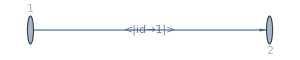

```mathematica
Blobs = {
<|
"id"->1,
"external_vertices"->{1,2},
"lmb_edge_indices"->{1},
"graph"->DirectedGraph[{
DirectedEdge[1,2,<|"id"->1|>]
}]
|>
};
Table[ShowClassicalGraph[b["graph"],Highlight->False,Size->300],{b,Blobs}]//Row
```

General all classical abelian 2->2 graphs using them, first tagging nothing so that the iso check merges a maximum and also symmetrizing over bottom and top attachments since we will de-symmetrize during equivalence class generation
Note that we must keep the self-energies at this stage, since the de-symmetrization over attachements later will generate non-self-energy contributions

```mathematica
TwoLoopClassicalGraphs=GenerateLoopGraphs[Blobs,
tagExternal->False,tagBlobs->False,tagBlobType->False,
tagTopLine->False,tagBotLine->False,
symmmetrizeTopLine->True,symmmetrizeBotLine->True,
Only1PI->False,MarkTopLine->True,MarkBotLine->True,
nLoops->2,topNPropRange->{0,4},botNPropRange->{0,4}
];
```

```mathematica
TwoLoopClassicalGraphs//Length
```

10

This leads to ten graphs, which will be the seed for the equivalence class identification and de-symmetrization

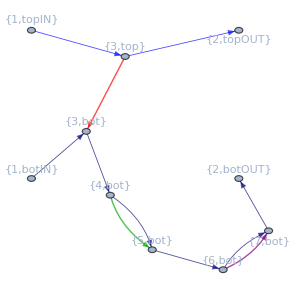
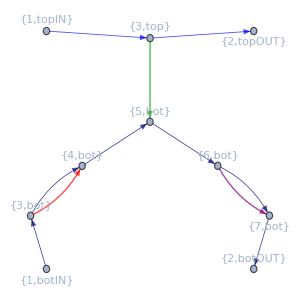
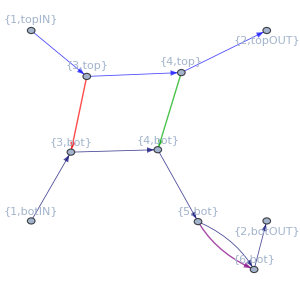
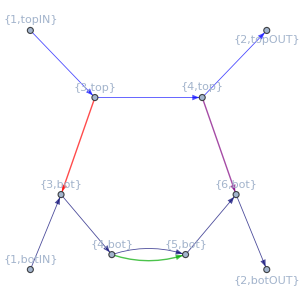
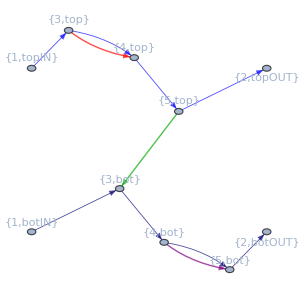
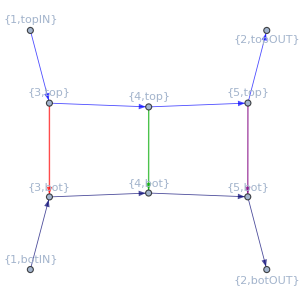
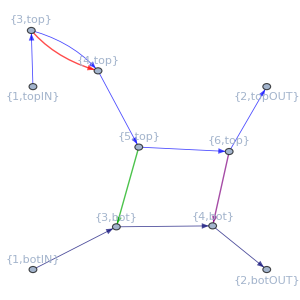
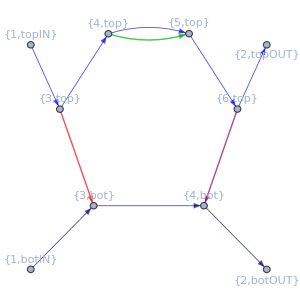
Graph #1
-Graphics- | Graph #2
-Graphics- | Graph #3
-Graphics- | Graph #4
-Graphics- | Graph #5
-Graphics-
Graph #6
-Graphics- | Graph #7
-Graphics- | Graph #8
-Graphics- | Graph #9
-Graphics- | Graph #10
-Graphics-
 |  |  |  |

```mathematica
ShowClassicalGraphs[TwoLoopClassicalGraphs,Size->{300,300},Ncolumns->5]
```

We are now ready to identify and populate with de-symmetrization the equivalence classes

```mathematica
TwoLoopClasses=IdentifyEquivalenceClasses[TwoLoopClassicalGraphs,{generateTopSymmetricGraphs->True,generateBotSymmetricGraphs->True,symmmetrizeTopLine->True,symmmetrizeBotLine->True,
shrinkTopLine->False,shrinkBotLine->False,tagExternal->True,tagBlobType->False,tagBlobs->False,tagTopLine->False,tagBotLine->False,Only1PI->True,MarkTopLine->True, MarkBotLine->True}];
```

Which we can visualise as follows:

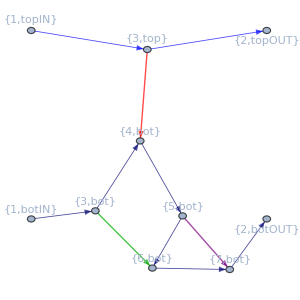
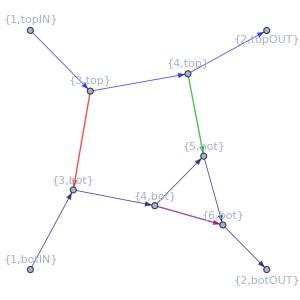
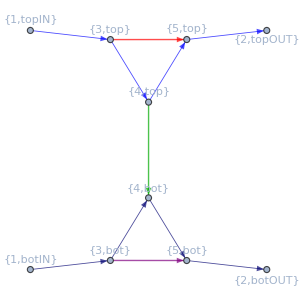
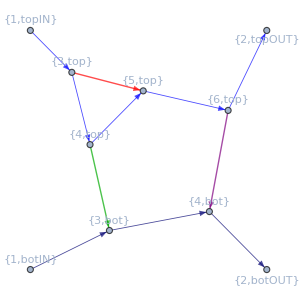
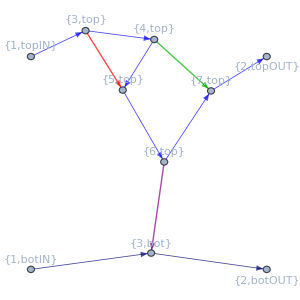
Class #1 (24 graphs)
-Graphics- | Class #2 (32 graphs)
-Graphics- | Class #3 (1 graphs)
-Graphics-
Class #4 (36 graphs)
-Graphics- | Class #5 (32 graphs)
-Graphics- | Class #6 (24 graphs)
-Graphics-
 |  |

```mathematica
ShowEquivalenceClasses[TwoLoopClasses,Size->{300,300}]
```

And we can show all graphs of the first class:

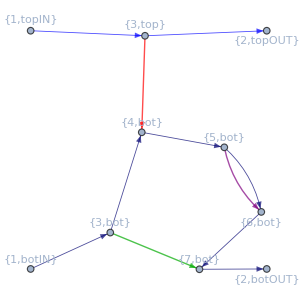
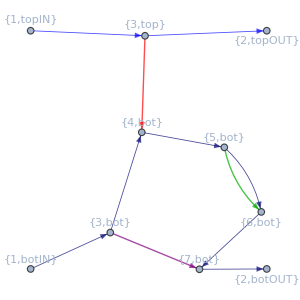
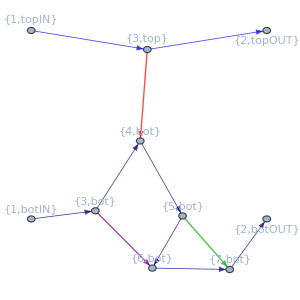
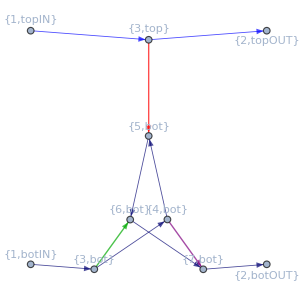
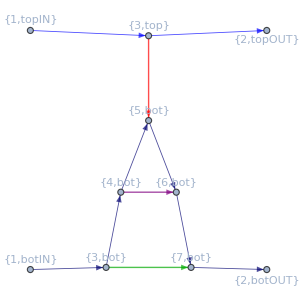
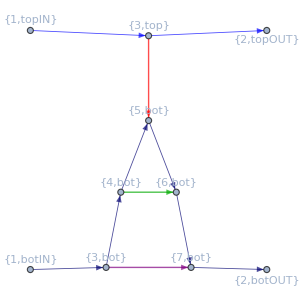
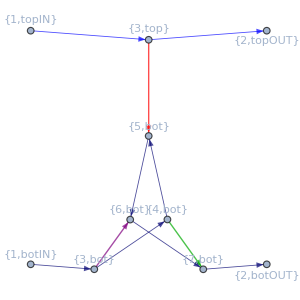
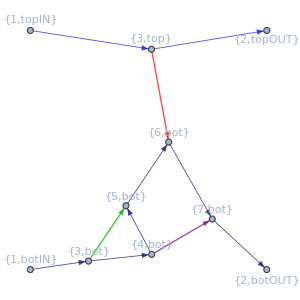
Graph #1
-Graphics- | Graph #2
-Graphics- | Graph #3
-Graphics- | Graph #4
-Graphics- | Graph #5
-Graphics-
Graph #6
-Graphics- | Graph #7
-Graphics- | Graph #8
-Graphics- | Graph #9
-Graphics- | Graph #10
-Graphics-
Graph #11
-Graphics- | Graph #12
-Graphics- | Graph #13
-Graphics- | Graph #14
-Graphics- | Graph #15
-Graphics-
Graph #16
-Graphics- | Graph #17
-Graphics- | Graph #18
-Graphics- | Graph #19
-Graphics- | Graph #20
-Graphics-
Graph #21
-Graphics- | Graph #22
-Graphics- | Graph #23
-Graphics- | Graph #24
-Graphics- |

```mathematica
ShowClassicalGraphs[TwoLoopClasses[Keys[TwoLoopClasses]⟦1(* first class! *)⟧],Size->{300,300},Ncolumns->5]
```

Or even one diagram in particular. Notice that the signatures are already written so as to facilitate the soft expansion!

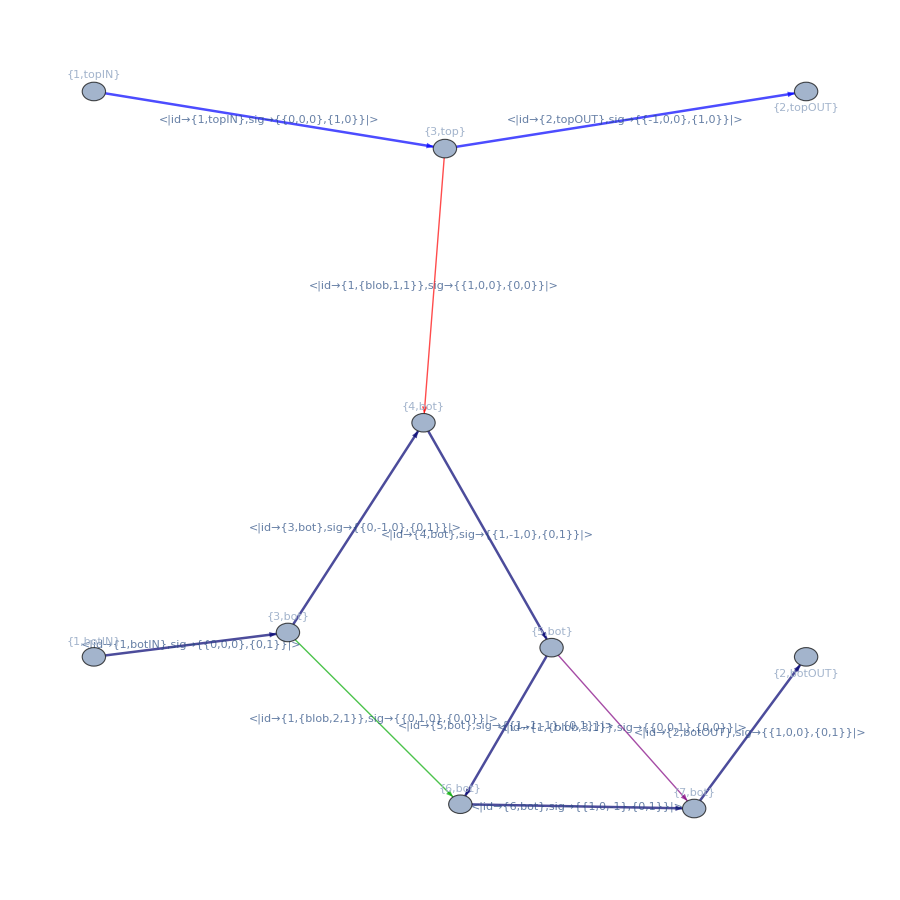

```mathematica
ShowClassicalGraph[TwoLoopClasses[Keys[TwoLoopClasses]⟦1(* first class! *)⟧]⟦1(* first diagram! *)⟧,Size->{900,900},eLabels->Automatic]
```

Now Generate all cuts for this particular graph:

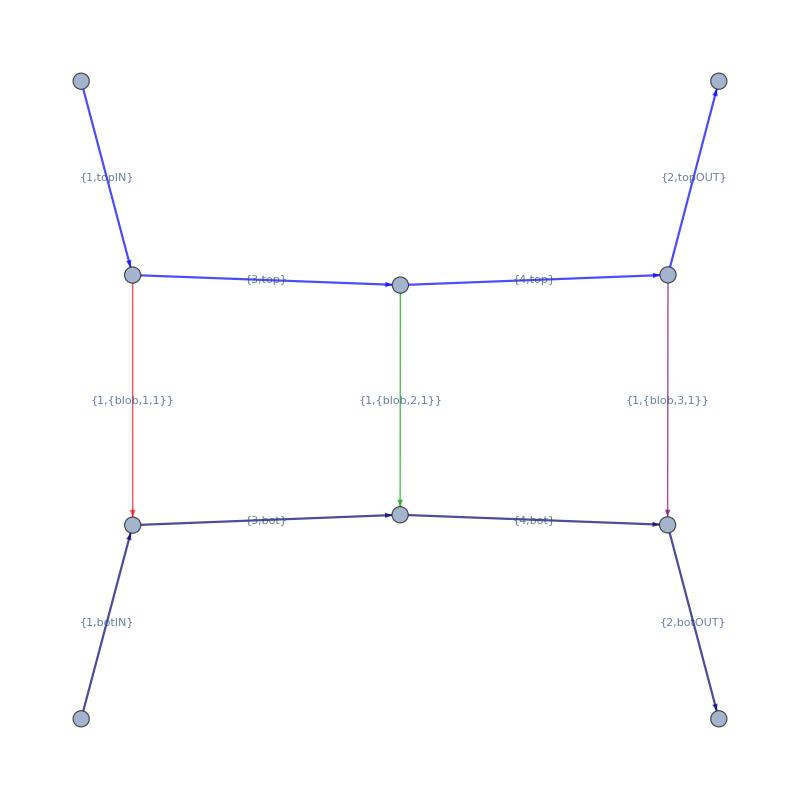

```mathematica
ShowClassicalGraph[TwoLoopClasses[Keys[TwoLoopClasses]⟦4⟧]⟦1⟧,vLabels->None,eLabels->"id", Size->800]
```

```mathematica
oneGraphCuts=GenerateAllCuts[TwoLoopClasses[Keys[TwoLoopClasses]⟦4⟧]⟦1⟧];
Length[oneGraphCuts]
```

4

Which we can easily visualize as follows:

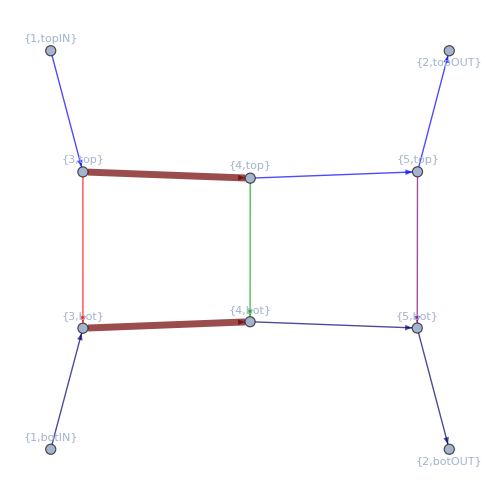
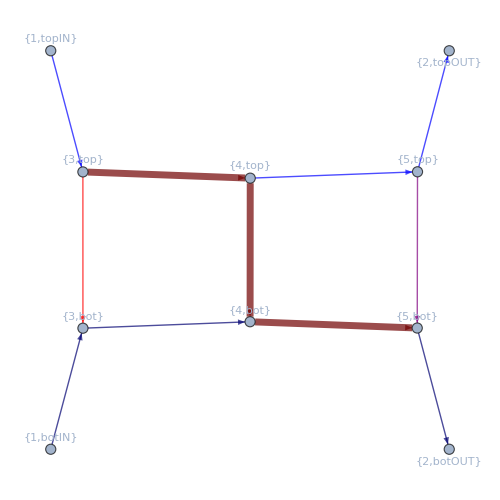
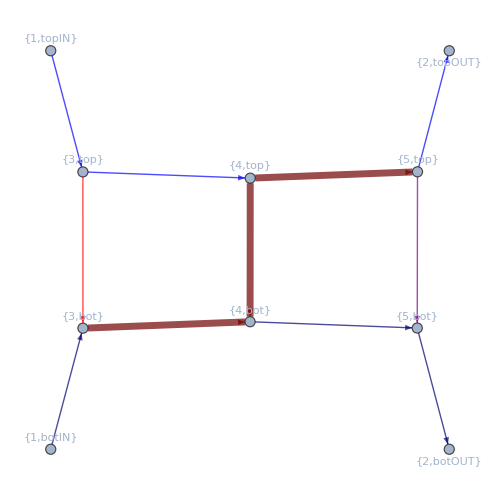
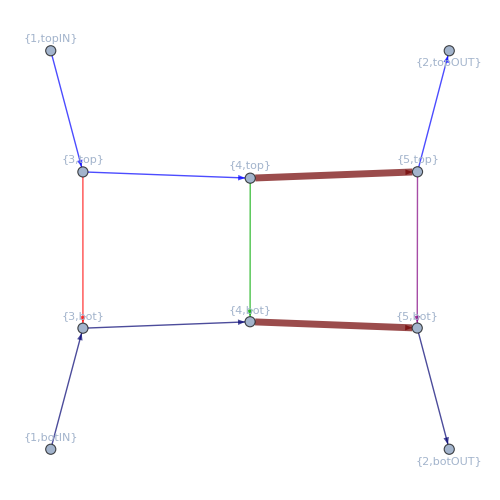
Cut #1 (2-cut)  [ {3, bot} | {3, top} ]
-Graphics- | Cut #2 (3-cut)  [ {1, {blob, 2, 1}} | {3, top} | {4, bot} ]
-Graphics-
Cut #3 (3-cut)  [ {1, {blob, 2, 1}} | {3, bot} | {4, top} ]
-Graphics- | Cut #4 (2-cut)  [ {4, bot} | {4, top} ]
-Graphics-
 |

```mathematica
ShowCuts[TwoLoopClasses[Keys[TwoLoopClasses]⟦4⟧]⟦1⟧,ccuts,Ncolumns->2,Size->{500,500}]
```

### Two-blob setup

Define the blob constituents

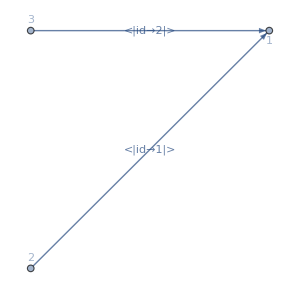
-Graphics--Graphics-

```mathematica
Blobs = {
<|
"id"->1,
"external_vertices"->{1,2},
"lmb_edge_indices"->{1},
"graph"->DirectedGraph[{
DirectedEdge[1,2,<|"id"->1|>]
}]
|>,
<|
"id"->2,
"external_vertices"->{1,2,3},
"lmb_edge_indices"->{1,2},
"graph"->DirectedGraph[{
DirectedEdge[2,1,<|"id"->1|>],
DirectedEdge[3,1,<|"id"->2|>]
}]
|>
};
Table[ShowClassicalGraph[b["graph"],Highlight->False,Size->300],{b,Blobs}]//Row
```

General all classical abelian 2->2 graphs using them, with default settings

```mathematica
TwoLoopClassicalGraphs=GenerateLoopGraphs[Blobs];
```

This leads to 24 graphs

```mathematica
TwoLoopClassicalGraphs//Length
```

24

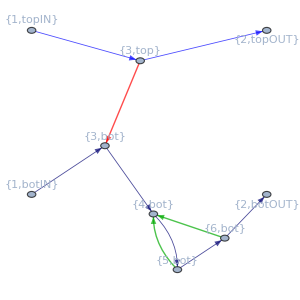
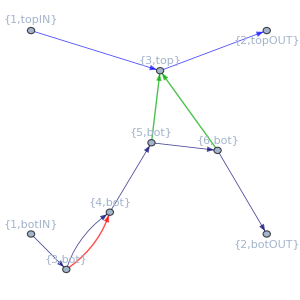
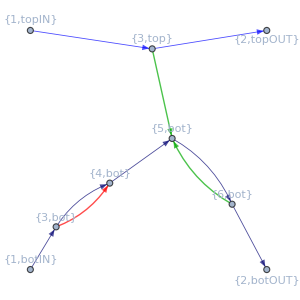
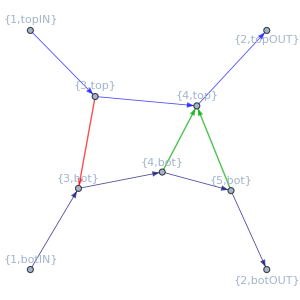
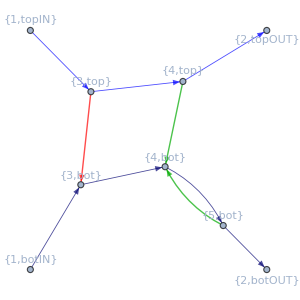
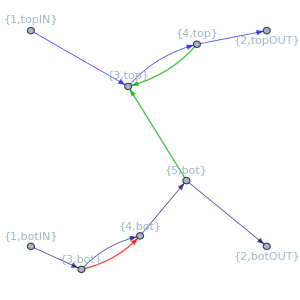
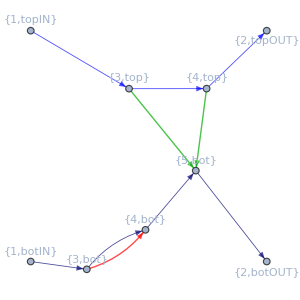
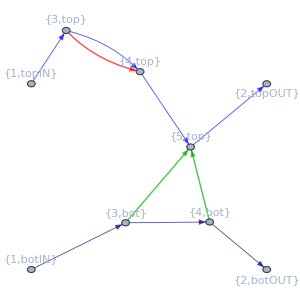
Graph #1
-Graphics- | Graph #2
-Graphics- | Graph #3
-Graphics- | Graph #4
-Graphics- | Graph #5
-Graphics-
Graph #6
-Graphics- | Graph #7
-Graphics- | Graph #8
-Graphics- | Graph #9
-Graphics- | Graph #10
-Graphics-
Graph #11
-Graphics- | Graph #12
-Graphics- | Graph #13
-Graphics- | Graph #14
-Graphics- | Graph #15
-Graphics-
Graph #16
-Graphics- | Graph #17
-Graphics- | Graph #18
-Graphics- | Graph #19
-Graphics- | Graph #20
-Graphics-
Graph #21
-Graphics- | Graph #22
-Graphics- | Graph #23
-Graphics- | Graph #24
-Graphics- |

```mathematica
ShowClassicalGraphs[TwoLoopClassicalGraphs,Size->{300,300},Ncolumns->5]
```

Which we can however merge into equivalence classes and desymmetrize top and botoom line

```mathematica
TwoLoopClasses=IdentifyEquivalenceClasses[TwoLoopClassicalGraphs];
```

Display the first graph with all details

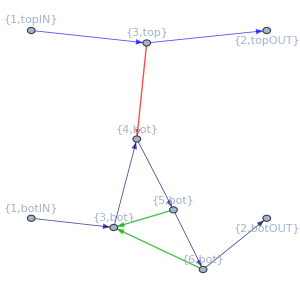
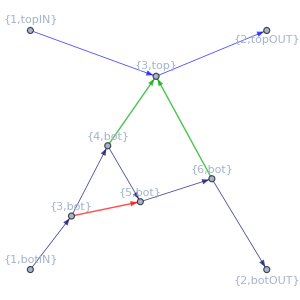
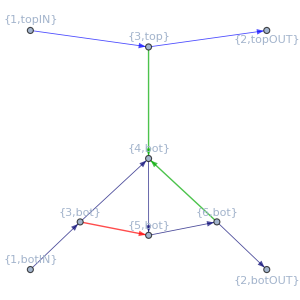
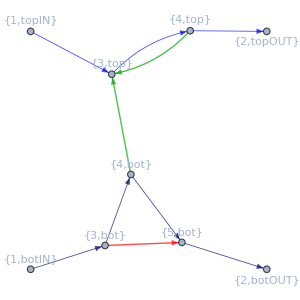
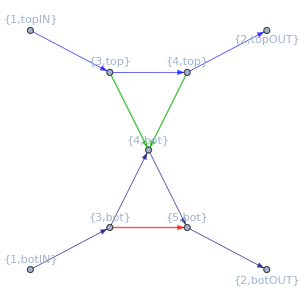
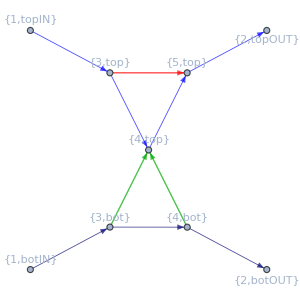
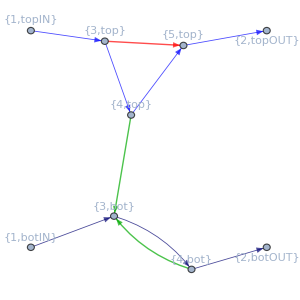
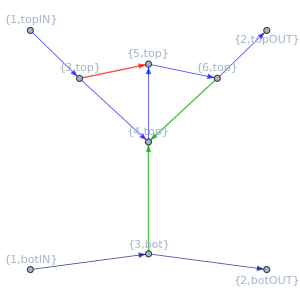
Class #1 (12 graphs)
-Graphics- | Class #2 (8 graphs)
-Graphics- | Class #3 (8 graphs)
-Graphics- | Class #4 (24 graphs)
-Graphics- | Class #5 (12 graphs)
-Graphics-
Class #6 (12 graphs)
-Graphics- | Class #7 (2 graphs)
-Graphics- | Class #8 (2 graphs)
-Graphics- | Class #9 (32 graphs)
-Graphics- | Class #10 (2 graphs)
-Graphics-
Class #11 (2 graphs)
-Graphics- | Class #12 (12 graphs)
-Graphics- | Class #13 (12 graphs)
-Graphics- | Class #14 (1 graphs)
-Graphics- | Class #15 (36 graphs)
-Graphics-
Class #16 (8 graphs)
-Graphics- | Class #17 (8 graphs)
-Graphics- | Class #18 (12 graphs)
-Graphics- | Class #19 (32 graphs)
-Graphics- | Class #20 (24 graphs)
-Graphics-
 |  |  |  |

```mathematica
ShowEquivalenceClasses[TwoLoopClasses,Size->{300,300},Ncolumns->5]
```

And as usual one can explore one particular graph:

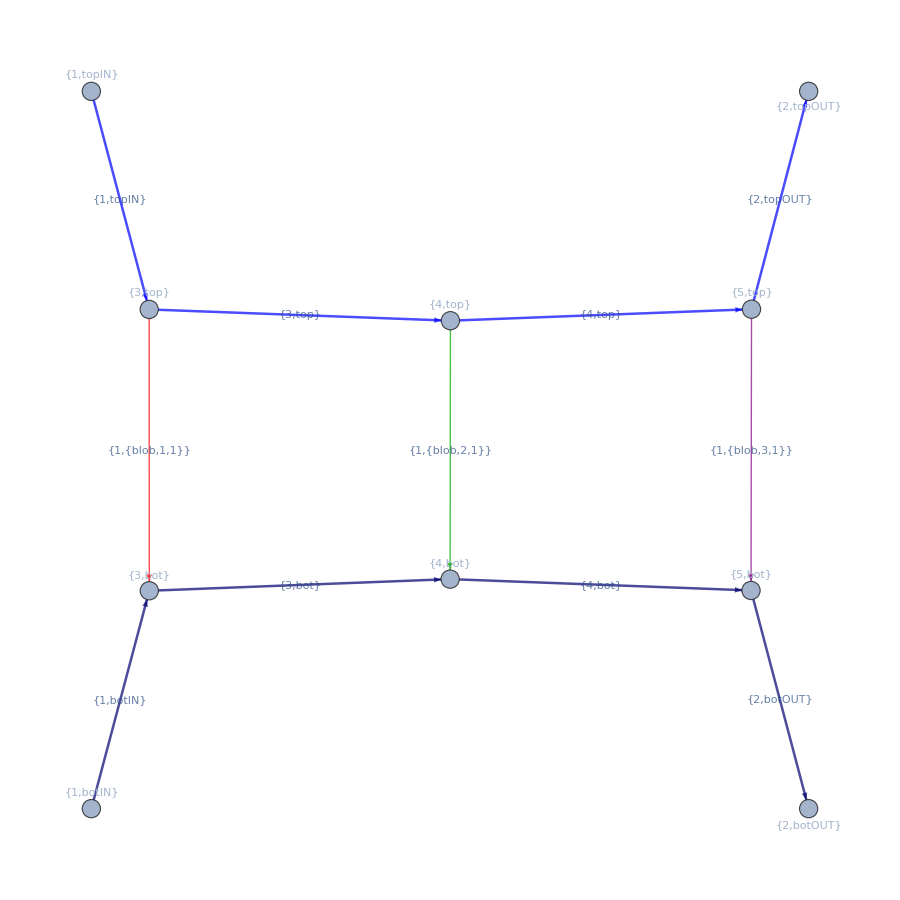

```mathematica
ShowClassicalGraph[TwoLoopClasses[Keys[TwoLoopClasses]⟦15⟧]⟦1⟧,Size->{900,900},eLabels->"id"]
```